## Contact Angle : Fluorinated SAM (square lattice 0.67,35.77) with SPCE water - 2000

### Import Data

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*PathMD="/Users/burbol/Downloads/g_rad_densmaps_all/";*)
PathMD="/Users/burbol/Downloads/";
input = Import[PathMD<>"g_rad_dmap_33pc_w1000_0.0ns_0.5ns.xvg","Table"];
Length[input]
```

1217

```mathematica
shift =5.04
```

5.04

```mathematica
(*shift =2.97;  (* 2g *)*)
```

```mathematica
(*shift =3.03;  (* 3g *)*)
```

```mathematica
(*shift =3.07;  (* 4g *)*)
```

```mathematica
(*shift =2;  (* 6g *)*)
```

```mathematica
(*PathMD="/Users/burbol/Downloads/g_rad_densmaps_all/";*)
(*input = Import[PathMD<>"g_rad_dmap_33pc_w1000_0.0ns_0.5ns.xvg","Table"];*)
start = 0;
Do[If[input[[i]] == {"#radius(nm)"},start=i],{i,1,Length[input]}];
data = Take[input,{start+1,Length[input]}]; (* extracted data *)
slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; 
 nslices = Length[slices];
sliceWidth = slices[[2]]-slices[[1]];
Do[slices[[i]] = slices[[i]] + sliceWidth*0.5,{i,1,Length[slices]}];
```

```mathematica
nslices
```

200

53

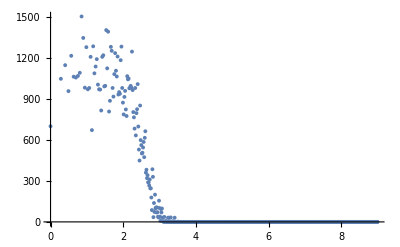

```mathematica
checkslice=53 (* Which slice to show *)
ListR=Table[{data[[i,1]],data[[i,checkslice+1]]},{i,1,Length[data]}];
ListPlot[ListR,Joined->False,PlotRange->All]
```

### Sanity Check

200

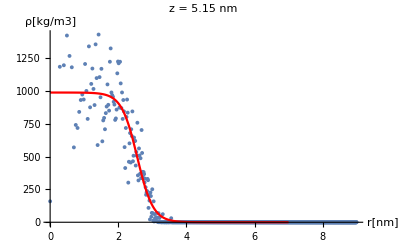

```mathematica
slices;
nslices

Clear[R,d,ρ]
checkslice = 52;
fitdata=Table[{0,0},{i,1,Length[data]}];
Do[fitdata[[i,1]]=data[[i,1]];fitdata[[i,2]]=data[[i,checkslice+1]],{i,1,Length[data]}];
plotdata = ListPlot[fitdata,PlotRange-> {{0,7},{0,1500}}];
fitparam=FindFit[fitdata,ρ/2(1-Tanh[2*(r-R)/d]),{{ρ,1000},{R,3},{d,1}},r];
plotfit = Plot[ρ/2(1-Tanh[2*(r-R)/d])/.fitparam,{r,0,7},PlotRange-> {{0,5},{0,1500}},PlotStyle->Red];
Show[plotdata,plotfit,AxesLabel->{"r[nm]","ρ[kg/m3]"},PlotLabel->"z = "<>ToString[slices[[checkslice]]]<>" nm",PlotRange->All]
```

### Determining the equimolar dividing planes

```mathematica
Clear[fp,ρ,n,i]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

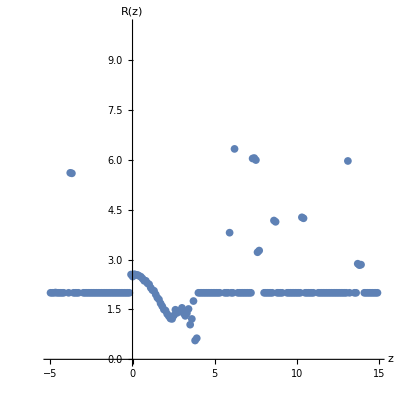

```mathematica
radius=Table[{slices[[i]]-shift,0},{i,1,nslices}];
fitdata=Table[{0,0},{i,1,Length[data]}];
Do[fitdata[[i,1]]=data[[i,1]],{i,1,Length[data]}]
Do[Do[fitdata[[i,2]]=data[[i,n+1]],{i,1,Length[data]}];fp=FindFit[fitdata,ρ/2(1-Tanh[2*(r-R)/d]),{{ρ,100},{R,2},{d,2.0}},r,MaxIterations->10000];
radius[[n,2]]=R/.fp,{n,1,nslices}];
plotradius=ListPlot[radius,AxesLabel->{"z","R(z)"},PlotRange-> {All,{0,10}},AspectRatio-> 1]
```

```mathematica
,
```

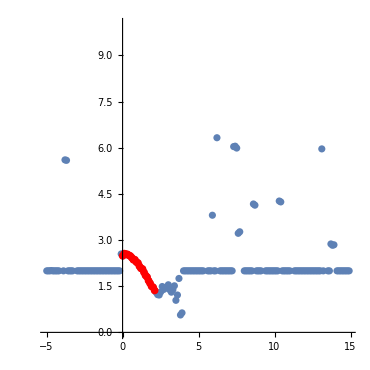

```mathematica
rad = Take[radius,{51,72}];
plotradius=ListPlot[radius,PlotRange-> All,AspectRatio-> 1,AxesOrigin->{0,0}];
plotrad=ListPlot[rad,PlotRange-> All,AspectRatio-> 1,AxesOrigin->{0,0},PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}];
Show[plotradius,plotrad,AspectRatio-> 1,PlotRange-> {All,{0,10}}]
```

```mathematica
Function to Fit a Circle with Least Squares
```

```mathematica
hypersphereFit[data_List]:=Module[{mat,rhs,qq,rr,params,cen},mat=Map[Append[#,1]&,data];
rhs=Map[#.#&,data];
{qq,rr}=QRDecomposition[mat];
params=LinearSolve[rr,qq.rhs];
params2={params[[1]],0,params[[3]]};
cen=Drop[params2,-1]/2;
{cen,Sqrt[Last[params]+cen.cen]}]
```

### Fitting a circle to the data

```mathematica
Clear[m]
```

{R→2.51189,m→-0.0877617}

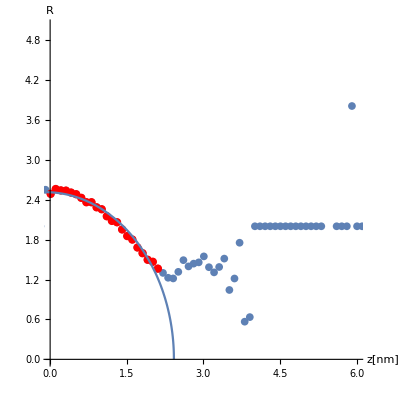

Base radius: 2.51035

```mathematica
fitcircle=FindFit[rad,Sqrt[R^2-(z-m)^2],{{R,2.1},{m,1}},z]
fitcircleplot = Plot[Sqrt[R^2-(z-m)^2]/.fitcircle,{z,-2,(R+m)/.fitcircle},PlotRange-> {{0,4.5},{0,5}},AspectRatio-> 1];
Show[plotradius,plotrad,fitcircleplot,AxesLabel->{"z[nm]","R"},AspectRatio->1,PlotRange-> {{0,6},{0,5}},AxesOrigin->{0,0}]
rb=√(fitcircle[[1,2]]^2-fitcircle[[2,2]]^2);
Print["Base radius: "<>ToString[rb]]
```

{{-0.337364,0},2.88544}

-0.337364

2.88544

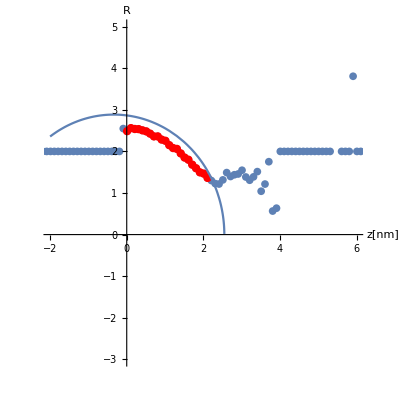

Base radius: 2.86565

```mathematica
resultfit=hypersphereFit[rad]
m2=resultfit[[1,1]]
R2=resultfit[[2]]
fitcircleplot = Plot[Sqrt[(R2)^2-(z-(m2))^2],{z,-2,7},PlotRange-> {{0,4.5},{0,5}},AspectRatio-> 1];
Show[plotradius,plotrad,fitcircleplot,AxesLabel->{"z[nm]","R"},AspectRatio->1,PlotRange-> {{-2,6},{-3,5}},AxesOrigin->{0,0}]
rb2=√(R2^2-m2^2);
Print["Base radius: "<>ToString[rb2]]
```

```mathematica
Interchange of the axes
```

```mathematica
rad;
rad1=rad[[All,1]];
rad2=rad[[All,2]];
newrad=Thread[{rad2,rad1}];
radius1=radius[[All,1]];
radius2=radius[[All,2]];
newradius=Thread[{radius2,radius1}];
```

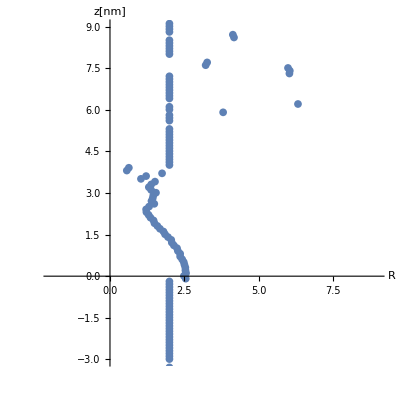

```mathematica
plotradius2=ListPlot[newradius,PlotRange-> {{-2,9},{-3,9}},AspectRatio-> 1,AxesOrigin->{0,0},AxesLabel->{"R","z[nm]"}]
```

```mathematica
Fit to circle with axes interchanged
```

```mathematica
First using new Circle Fit Function "hypersphereFit"
```

```mathematica
resultfit2=hypersphereFit[newrad]
R3=resultfit2[[2]];
m3=resultfit2[[1,1]];
```

{{-0.330897,0},2.88469}

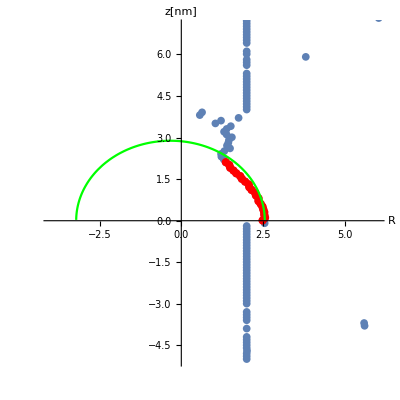

Base radius: 2.86565

z-coord of Circle Center: m= -0.330897

Circle Radius: 2.88469

```mathematica
fitcircleplot2 = Plot[Sqrt[(R3)^2-(z-(m3))^2],{z,-4,7},PlotRange-> {{0,4.5},{0,5}},AspectRatio-> 1,AxesOrigin->{0,0},PlotStyle->Green];
plotrad2=ListPlot[newrad,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}];
Show[plotradius2,plotrad2,fitcircleplot2,AxesLabel->{"R","z[nm]"},AspectRatio->1,PlotRange-> {{-4,6},{-5,7}},AxesOrigin->{0,0}]
rb3=√(R3^2-m3^2);
Print["Base radius: "<>ToString[rb3]]
Print["z-coord of Circle Center: m= "<>ToString[m3]]
Print["Circle Radius: "<>ToString[R3]]
```

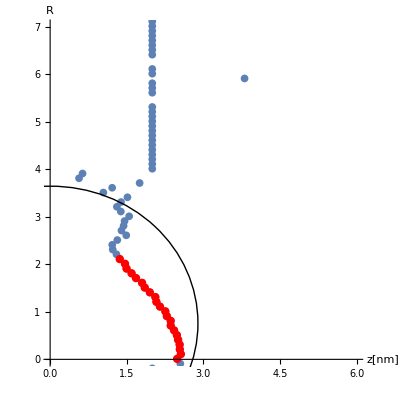

Base radius: 2.78027

z-coord of Circle Center: m= 0.769103

Circle Radius: 2.88469

```mathematica
bola2=Graphics[{Circle[{0,m3+1.1},R3]},Axes->True];
Show[plotradius2,plotrad2,bola2,AxesLabel->{"z[nm]","R"},PlotRange-> {{0,6},{0,7}},AxesOrigin->{0,0}]
rb3=√((R3)^2-(m3+1.1)^2);
R4=R3;
m4=m3+1.1;
Print["Base radius: "<>ToString[rb3]]
Print["z-coord of Circle Center: m= "<>ToString[m4]]
Print["Circle Radius: "<>ToString[R4]]
```

```mathematica
(*fitcircle2=FindFit[newrad,{Sqrt[Rc^2-x^2]+m},{{Rc,4.5},{m,0.9}},x]
fitcircleplot2 = Plot[Sqrt[fitcircle2[[1,2]]^2-x^2]+fitcircle2[[2,2]],{x,-2,(Rc+m)/.fitcircle2},PlotRange-> {{0,4.5},{0,5}},AspectRatio-> 1];
Show[plotradius,plotrad,fitcircleplot2,AxesLabel->{"z[nm]","R"},AspectRatio->1,PlotRange-> {{0,6},{0,5}}]
rb3=√(fitcircle2[[1,2]]^2-fitcircle2[[2,2]]^2);
Print["Base radius: "<>ToString[rb3]]*)
```

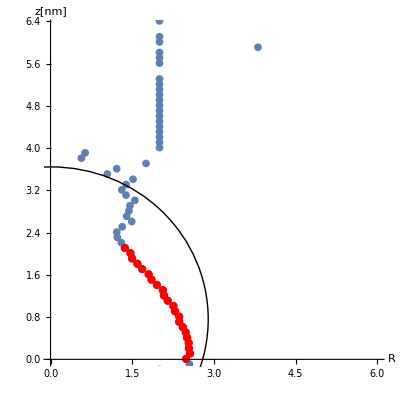

fitcircle2

```mathematica
(*Plot[Sqrt[fitcircle[[1,2]]^2-x^2]+fitcircle[[2,2]],{x,-2,7},PlotRange-> {{-3,4.5},{-3,5}},AspectRatio-> 1]*)
bola=Graphics[{Circle[{0,m4},R4]},Axes->True];
Show[plotradius2,plotrad2,bola,AxesLabel->{"R","z[nm]"},AspectRatio->1,PlotRange-> {{0,6},{0,6.3}}]
fitcircle2
```

### Fitting line

```mathematica
radfit
```

{{3.306,3.0362},{3.366,3.03031},{3.426,2.94799},{3.486,2.974},{3.546,2.93017},{3.606,2.90138},{3.666,2.9075},{3.726,2.88706},{3.786,2.84854},{3.846,2.8095},{3.906,2.82007},{3.966,2.76405},{4.026,2.69675},{4.086,2.70498},{4.146,2.65205}}

```mathematica
(* Contact angle *)
Θ=180-ArcCot[fitung[x0][[2,1]]]180/π
```

246.485

```mathematica
Θ=-ArcCot[fitung[x0][[2,1]]]180/π
```

66.485

```mathematica
rb=fitung[0]
```

4.48197

### Contact Angle

```mathematica
Θ = 90+(180/π )*ArcSin[newm/newRc]
```

145.18

```mathematica
Θ = 90+(180/π )*ArcSin[m/R]/.fitcircle
```

103.509

```mathematica
Θ = 90+(180/π )*ArcSin[m2/R2]
```

102.501

```mathematica
Θ = 90+(180/π )*ArcSin[m3/R3]
```

88.0294

```mathematica
Θ = 90+(180/π )*ArcSin[m4/R4]
```

101.935

```mathematica
Θ = 90+180/π ArcTan[m/Sqrt[R^2-m^2]]/.fitcircle
```

103.509

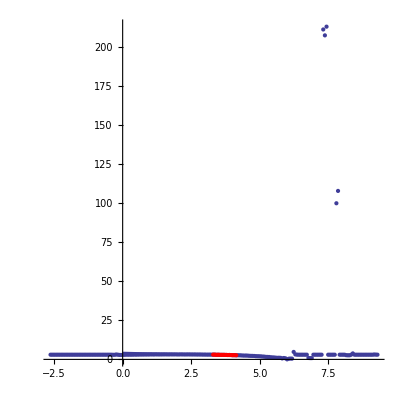

```mathematica
radfit=Take[rad,{1,15}];
sl2=ListPlot[radfit,PlotRange->All,PlotStyle->Red];
fitung[x0_]=Fit[radfit,{1,x},x]/.x->x0;sl3=Plot[fitung[x],{x,0,3}];
Show[plotradius,sl3,sl2,AspectRatio->1,PlotRange->Automatic]
```

```mathematica
Tabθrb=Append[Tabθrb,{rb,Θ}]
```

{{2.07343,141.204}}

```mathematica
Tabθrb={};
```

```mathematica
(* Analysing data *)
```

-0.389693-0.808 x0

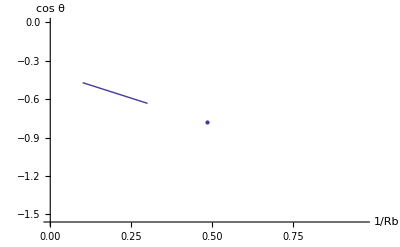

```mathematica
Tab1=Table[{1/Tabθrb[[i,1]],Cos[π/180 Tabθrb[[i,2]]]},{i,1,Length[Tabθrb]}];
pic1=ListPlot[Tab1,AxesLabel->{"1/Rb","cos θ"}];
ff[x0_]=Fit[Tab1,{1,x},x]/.x->x0
pic2=Plot[ff[x0],{x0,0.1,0.3}];
Show[pic1,pic2]
```

```mathematica
Tabθrb
```

{}

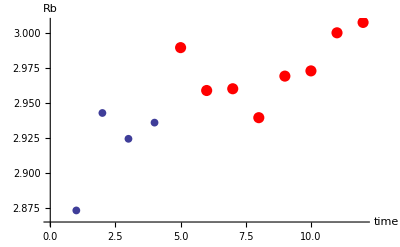

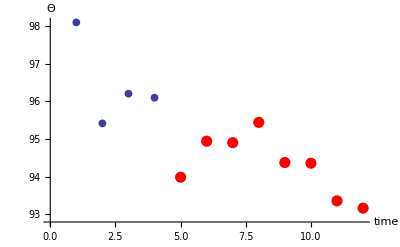

Rb = 2.97491 ± 0.00867458

θ = 94.3174 ± 0.297876

```mathematica
FromI=5;
ToI=Length[Tabθrb];
Tab1=Table[{i,Tabθrb[[i,1]]},{i,1,Length[Tabθrb]}];
TabPick1=Take[Tab1,{FromI,ToI}];
xx1=ListPlot[Tab1,AxesLabel->{"time","Rb"},PlotStyle->PointSize[0.014]];
xx2=ListPlot[TabPick1,AxesLabel->{"time","Rb"},PlotStyle->{PointSize[0.02],Red}];
Tab1=Table[{i,Tabθrb[[i,2]]},{i,1,Length[Tabθrb]}];
xx3=ListPlot[Tab1,AxesLabel->{"time","Θ"},PlotStyle->PointSize[0.014]];
TabPick2=Take[Tab1,{FromI,ToI}];
xx4=ListPlot[TabPick2,AxesLabel->{"time","Rb"},PlotStyle->{PointSize[0.02],Red}];
Show[xx1,xx2]
Show[xx3,xx4]
Print["Rb = ",Mean[TabPick1][[2]]," ± ",StandardDeviation[TabPick1][[2]]/√(Length[TabPick1]-1)]
Print["θ = ",Mean[TabPick2][[2]]," ± ",StandardDeviation[TabPick2][[2]]/√(Length[TabPick2]-1)]
```

```mathematica
Export[folder<>"contour_data.dat",Table[{rad[[i,2]],rad[[i,1]]},{i,1,Length[rad]}]];
Export[folder<>"contour_fit.dat",Table[{Sqrt[R^2-(z-m)^2]/.fitcircle,z},{z,0,(R+m+0.002)/.fitcircle,0.001}]];
```

StringJoin::string: String expected at position 1 in folder.

Export::chtype: First argument folder is not a valid file specification.

StringJoin::string: String expected at position 1 in folder.

Export::chtype: First argument folder is not a valid file specification.

```mathematica
(* First measurement of Θ, 2.May *)
TabΘα={{1,26,2},{0.8,65,5},{0.6,88,3},{0.4,100,5},{0.2,120,5},{0,125,5}};
```

```mathematica
(* contact.1r - 6r, Measurement of Θ, 28.Feb 2013 *)
TabΘα={{1,0,0},{0.8,60,6},{0.6,95,4},{0.4,113,5},{0.2,117,5}};
(* za 0.7 se sklepa, da je θ okoli 80° *)
```

```mathematica
(* contact.1g - 7g, Measurement of Θ, 9.Apr 2013, 14 May; 9g:  18 Jun 2013 *)
TabΘα={{1.0,0,0},{0.8,10.9,2},{0.7,84,4},{0.6,102,2},{0.4,125,5},{0.2,139,3},{0,142,2},{0.75,59.3,1.5}};
```

```mathematica
(* contact.1f - 7f, Measurement of Θ, 6.Aug 2013 *)
TabΘα={{0.8,34.5,0.6},{0.7,90,5},{0.6,100,2}};
```

```mathematica
(* system contact.D1.1o2-big *)
TabΘ={58.738483551443835,56.573812157404454,55.20048218584333,55.5913206461983,57.627772165366544};
```

{58.7385,56.5738,55.2005,55.5913,57.6278}

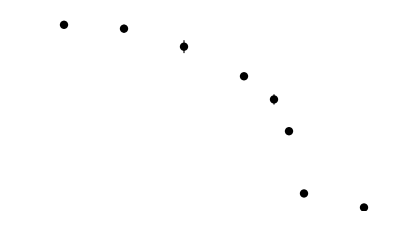

```mathematica
picΘ=ErrorListPlot[TabΘα,AxesLabel->{"q(OH)","Θ"}]
```

```mathematica
Export["~/Documents/Raziskave/Gromacs/BergLimit/DataFig/contact-drop-g.dat",Append[TabΘα,{}]]
```

~/Documents/Raziskave/Gromacs/BergLimit/DataFig/contact-drop-g.dat

```mathematica
40^(1/3.)
```

3.41995

```mathematica
(* 2g *)
Tabrbθ={{4.87,17.1,1},{6.00,14.6,1}};
```

```mathematica
(* 3g *)
Tabrbθ={{2.97,94.3,0.6},{3.303,94,0.2},{3.590,96.2,0.2}};
```

```mathematica
(* 4g *)
Tabrbθ={{2.907,116.9,0.2},{2.68,115.8,0.2},{2.39,116.3,0.5}};
```

```mathematica
(* 6g *)
Tabrbθ={{1.88,133.3,0.2},{2.07,133.5,0.5},{2.238,134.3,0.1}};
```

```mathematica
(* 7g *)
Tabrbθ={{4.119,77.6,0.2},{3.27,77.9,1.6}};
```

```mathematica
Tab0=Table[{1/Tabrbθ[[i,1]],Cos[Tabrbθ[[i,2]]π/180.],Sin[Tabrbθ[[i,2]]π/180.]Tabrbθ[[i,3]]π/180.},{i,1,Length[Tabrbθ]}]
```

{{0.343997,-0.452435,0.00311296},{0.373134,-0.435231,0.00314271},{0.41841,-0.443071,0.00782332}}

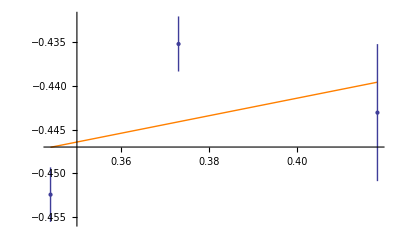

coeff x^0 = -0.481406 ± 0.0188438

coeff x^1 = 0.0999349 ± 0.0493003

value at 0: -0.483721 ± 0.0188438

```mathematica
ErrorFit[Tab0,1,0]
```

```mathematica
Print["θ = ",Re[ArcCos[coeffI[0]]180/π]," ± ",Abs[(Re[ArcCos[coeffI[0]]-ArcCos[coeffI[0]-coeffIerr[0]]])180/π]]
Print["τ = ",-1/16.61 γ coeffI[1]," ± ",Abs[1/16.61 γ coeffIerr[1]]," kJ/mol nm"]
```

θ = 118.777 ± 1.23925

τ = -3.3091 ± 1.63246 kJ/mol nm

#### θ(time) - storage

```mathematica
(* contact.2r *)
TabΘ=
{53.988976866901524,54.77783646894886,55.130471110059624,55.170712255508064,56.12102049247143,56.307780558587694,57.35207121370904,58.92836020286074,64.35097963827278,68.19597866910586,61.01564799365798,76.82162200934958};
```

```mathematica
(* contact.3r, 14.8.2013 *)
TabΘ={102.81310741453814,98.95457005596776,96.10944571721711,94.99328310627044,93.13763508611909,90.7044905491423,90.62602781209529,90.46043569104371,90.2491503871905,90.3553826645951,91.31651792517623,89.73974348198246,89.06548630731332,87.67408243421633,87.271184682376,87.89345226796114,88.49907063247069,88.55022847055855,89.05816161305441,90.74470602349756,91.03535132445616,90.63595889361703,91.82020055514666,92.07365525073944,91.82478263851795,91.6860527676726}
```

```mathematica
(* contact.3r.1, 14.8.2013 *)
TabΘ={101.04594112672588,97.69489048637871,94.07482008639792,91.55223824259554,91.09699814559565,89.9453459088425,89.34877491110144,88.35621234241492,87.8889675758757,88.8956972846932,88.36863539802933,89.40017729705308,90.10246096717171,89.48291120146382,89.36704283085162,88.73221249836327};
```

```mathematica
(* contact.4r *)
TabΘ={116.65869993348619,114.7557708865759,113.39084095314428,113.6673201444421}
```

{116.659,114.756,113.391,113.667}

```mathematica
(* contact.5r *)
TabΘ={125.39676276988729,123.64136504242208,122.34943334817936,121.1577088754286,120.68935130883668,119.13459677975095,119.11838313853896,118.79133237655154,117.96669236927977,117.11731699502313}
```

```mathematica
(* contact.7r, 13.8.2013 *)
TabΘ={93.76420749985776,89.25996480914033,86.07060138008013,84.10653394436711,80.72671567337588,78.07286572993988,77.02579760586599,76.05448509653928,73.57487608547842,71.84366434839582,71.74296013156214,71.84880069937462,71.4013939784238,70.47479191111056,70.01498726133693,69.78736865868294};
```

```mathematica
(* contact.7r.1, 13.8.2013 *)
TabΘ={89.894556683804,83.91348027466445,80.02342630946595,76.56291134724339,74.99254823006977,72.57842694289488,71.84213396644091,71.49525688933397,72.22823093416727,73.18490337833515,70.76275583188222,70.1594699959658,71.51860000588586,73.09417432376306,73.06541201242642,73.08159938362829,73.6843645591881}
```

```mathematica
(* contact.7r.3, 13.8.2013 *)
TabΘ={65.9430405842123,63.95810719561655,64.9380681370244,67.90616893814115,65.69117406644594};
```

```mathematica
(* line tension - θ(rb): {rb,θ,δθ}: 7r *)
Tabrbθ={{2.49,66,2},{2.81,75,1},{3.28,72.2,1.1},{3.9,70,2}}
```

{{2.49,66,2},{2.81,75,1},{3.28,72.2,1.1},{3.9,70,2}}

```mathematica
(* line tension - θ(rb): {rb,θ,δθ}: 3r *)
Tabrbθ={{3.3,90.1,1},{3.03,89,1},{2.4,92,2},{2.15,90,2}};
```

```mathematica
(* contact.6r *)
TabΘ={131}
```

```mathematica
(*********** g ***********)
```

```mathematica
(* contact.2g *)
TabΘ={64.05304892517958,66.79262489145358,65.36974514652452,66.48256525718587,65.79095287578683,63.48960965438079}
```

{64.053,66.7926,65.3697,66.4826,65.791,63.4896}

```mathematica
(* contact.7g *)
TabΘ={84.21693009004264,82.1049434227889,80.62986292443809,84.63037478502683,85.61213855803629,88.33553229989123}
```

```mathematica
(* contact.3g *)
TabΘ={103.79709758081513,101.40310602111391,102.15415031324586,101.3646547097462,101.82411049934727,103.76767155651369}
```

```mathematica
(* contact.6g *)
TabΘ={143.63017876411658,143.3270068807083,143.24430423507826,142.1984050079966,142.09242648479795}
```

```mathematica
(*********** gH ***********)
```

```mathematica
(* contact.9gH *)
Tabθrb={{4.1479533453138595,76.46261798289915},{4.176236372287634,75.83081436658567},{4.217944286504681,74.48608460454298},{4.2237605471899125,74.40034689612506},{4.235352618316397,74.26583784462913},{4.221971924437019,74.32546282686977},{4.236793337010672,73.89881900258494}};
```

```mathematica
(* contact.9gH.1 *)
Tabθrb={{3.6032781574451453,73.89881900258494},{3.6869233289393746,75.55367498135246},{3.736891444885608,74.09003664895323},{3.7255406982692034,74.23654335158962},{3.725812180230499,74.12503288480573},{3.798214810630075,71.71903058634183},{3.7878502660340643,71.84375982667268},{3.791509414799738,71.875910254104},{3.7849543543857718,72.14786974990781},{3.7899931736497803,72.05284708447834},{3.786383072350984,71.82982261285318}};
```

```mathematica
(* contact.9gH.2 *)
Tabθrb={{3.2993278963192485,75.44974844320238},{3.3167112565943735,74.65375618731562},{3.3077373952303137,74.9758363532542},{3.3503878860744747,73.65869896947595},{3.3549662866011634,73.2496518662391},{3.3314461770146946,74.1992209113681},{3.381087097413774,72.08194662141261},{3.3610645399770274,72.96174867088074},{3.3657994400596047,73.04760383001471},{3.3616437249745554,73.2775038692046},{3.3632240415375194,73.23449224431565},{3.3988249678315636,71.74531718914044}};
```

```mathematica
(* contact.9gH.3 *)
Tabθrb={{2.965294776660243,72.9311340793902},{2.9706304196994786,72.78891497985391},{2.9439844787450102,74.08033086994953},{2.93681778296507,74.42633983824946},{3.006871823035709,71.17879245357605},{3.045422711778699,69.08789511390827}};
```

```mathematica
(* contact.2f *)
TabΘ={33.81914517636088,34.68995722063159,34.45821424356892,34.52291205717636,34.75896543031742,35.48005964279476,33.83940389932612}
```

```mathematica
(* contact.3f *)
TabΘ={105.76474621068162,104.65319838855038,102.21344567119162,101.8195360420584,99.248480942693}
```

### Line-tension correction

```mathematica
(* Predicting base radius - from spherical cap *)
V=4142/c0; (* droplet volume in nm^3 *)
θmin=85.; (* microscopic angle *)
Rb=(3V/π /((1-Cos[θmin π/180])/Sin[θmin π/180](1+(1-Cos[θmin π/180])/Sin[θmin π/180]^2)))^(1/3)
```

4.08018

```mathematica
σ=10; (*in kJ/mol nm *)
γ=33; (* in kJ/mol nm^2 *)
Rb=4; (* base radius in nm*)
θmin=60.; (* microscopic angle *)
```

```mathematica
(* corrected macroscopic contact angle *)
ArcCos[Cos[θmin π/180]+σ/(γ Rb)]180./π
```

80.7104

### Fitting an ellipsoid to the data

```mathematica
Clear[a,b]
```

FindFit::nrlnum: The function value {-2.27352 + 2.5717\ ⅈ, -2.30911 + 2.44536\ ⅈ, -2.34682 + 2.31402\ ⅈ, -2.35786 + 2.1792\ ⅈ, -2.38756 + 2.04251\ ⅈ, « 3 », -2.3874 + 1.42355\ ⅈ, -2.36889 + 1.23944\ ⅈ, -2.35313 + 1.03572\ ⅈ, -2.32202 + 0.787908\ ⅈ, -2.29375 + 0.433859\ ⅈ} is not a list of real numbers with dimensions {13} at {a, b, m} = {2.10565, -1.32738, 2.47326}.

{a→2.10565,b→-1.32738,m→2.47326}

-Graphics-

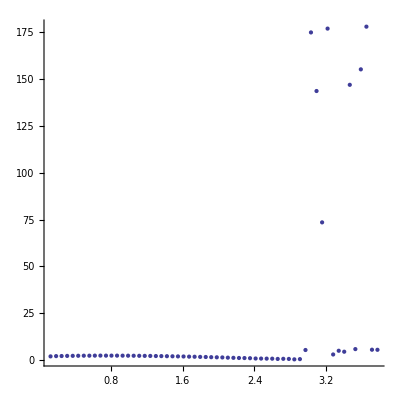

```mathematica
fitellipsoid=FindFit[rad,a*Sqrt[1-(z-m)^2/b^2],{{a,2.4},{b,2.4},{m,0.16}},z]
fitellipsoidplot = Plot[a*Sqrt[1-(z-m)^2/b^2]/.fitellipsoid,{z,0,(b+m)/.fitellipsoid},PlotRange-> {{0,4},{0,6}},AspectRatio-> 1]
Show[plotradius,fitellipsoidplot]
```

### Contact Angle

```mathematica
Subscript[Θ, e] = 90+180/π ArcTan[m*a/(b*Sqrt[b^2-m^2])]/.fitellipsoid
```

70.9567

```mathematica
Subscript[r, 0,e]=a* Sqrt[1-(m/b)^2]/.fitellipsoid
```

2.61735

```mathematica
ContactAngle[file_,startslice_,endslice_,shift_,initialR_,initialm_]:=Module[{input,start,data,slices,nslices,sliceWidth,radius,fitdata,fp,rad,plotradius,fitcircle,fitcircleplot},
input = Import[file,"Table"];
start = 0;
Do[If[input[[i]] == {"#radius(nm)"},start=i],{i,1,Length[input]}];
data = Take[input,{start+1,Length[input]}];
slices = Drop[(Take[input,{start-1,start-1}])[[1]],{1,2}]; 
nslices = Length[slices];
sliceWidth = slices[[2]]-slices[[1]];
Do[slices[[i]] = slices[[i]] + sliceWidth*0.5,{i,1,Length[slices]}];

radius=Table[{slices[[i]]-shift,0},{i,1,nslices}];
fitdata=Table[{0,0},{i,1,Length[data]}];
Do[fitdata[[i,1]]=data[[i,1]],{i,1,Length[data]}];

Do[Do[fitdata[[i,2]]=data[[i,n+1]],{i,1,Length[data]}];fp=FindFit[fitdata,ρ/2(1-Tanh[2*(r-R)/d]),{{ρ,1000},{R,1},{d,0.5}},r];radius[[n,2]]=R/.fp,{n,1,nslices}];

rad = Take[radius,{startslice,endslice}];
fitcircle=FindFit[rad,Sqrt[R^2-(z-m)^2],{{R,initialR},{m,initialm}},z];

{90+180/π ArcTan[m/Sqrt[R^2-m^2]]/.fitcircle,Sqrt[R^2-m^2]/.fitcircle}
]
```

```mathematica
scr = Table[0,{i,1,20}];
startslice =2;
endslice = 41;
shift =1.192;
initialR = 3.0;
initialm = 1.8;
```

```mathematica
scr[[1]]=ContactAngle[folder<>"rad_density_0-1ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[2]]=ContactAngle[folder<>"rad_density_1-2ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[3]]=ContactAngle[folder<>"rad_density_2-3ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[4]]=ContactAngle[folder<>"rad_density_3-4ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[5]]=ContactAngle[folder<>"rad_density_4-5ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[6]]=ContactAngle[folder<>"rad_density_5-6ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[7]]=ContactAngle[folder<>"rad_density_6-7ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[8]]=ContactAngle[folder<>"rad_density_7-8ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[9]]=ContactAngle[folder<>"rad_density_8-9ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[10]]=ContactAngle[folder<>"rad_density_9-10ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[11]]=ContactAngle[folder<>"rad_density_10-11ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[12]]=ContactAngle[folder<>"rad_density_11-12ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[13]]=ContactAngle[folder<>"rad_density_12-13ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[14]]=ContactAngle[folder<>"rad_density_13-14ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[15]]=ContactAngle[folder<>"rad_density_14-15ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[16]]=ContactAngle[folder<>"rad_density_15-16ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[17]]=ContactAngle[folder<>"rad_density_16-17ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[18]]=ContactAngle[folder<>"rad_density_17-18ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[19]]=ContactAngle[folder<>"rad_density_18-19ns.xvg",startslice,endslice,shift,initialR,initialm]
scr[[20]]=ContactAngle[folder<>"rad_density_19-20ns.xvg",startslice,endslice,shift,initialR,initialm]
```

{137.612,1.65126}

{144.09,1.42046}

{143.969,1.42483}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{137.756,1.6394}

{139.798,1.56827}

{143.487,1.44166}

{140.396,1.55076}

{139.66,1.57419}

{140.724,1.53801}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{138.899,1.60129}

{141.464,1.51086}

{136.762,1.67098}

{138.523,1.6131}

{139.067,1.59399}

{136.45,1.6817}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{139.592,1.57738}

{145.853,1.35659}

{148.318,1.26632}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{142.131,1.48883}

{153.57,1.07169}

```mathematica
..
```

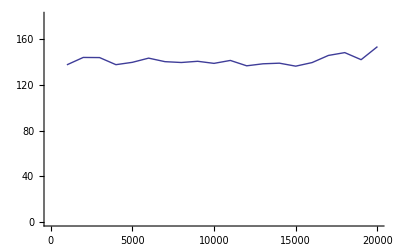

```mathematica
contactangletime = Table[{1000*i,scr[[i,1]]},{i,1,Length[scr]}];
ListPlot[contactangletime,PlotRange->{{0,20000},{0,180}},Joined->True]
```

```mathematica
contactangles = Table[scr[[i,1]],{i,1,Length[scr]}];
radii =Table[scr[[i,2]],{i,1,Length[scr]}];
```

```mathematica
Mean[contactangles]
Mean[radii]
```

141.406

1.51208

```mathematica
StandardDeviation[contactangles]
```

4.22068

```mathematica
StandardDeviation[radii]
```

0.150078

## From surface tension

```mathematica
ArcCosWett[x_]:=If[x<-1,π,If[x>1,0,ArcCos[x]]]
```

```mathematica
PathMD="~/.wine/drive_c/BergLimit/";
```

```mathematica
(* npr: frozen_D1.1p-#  18..21 *)
fromN=1;
toN=4;
For[i=fromN, i≤toN, i++,
frozTab[i]= Import[PathMD<>"frozen_D1.1q-"<>ToString[i]<>".dat","Table"]]
```

```mathematica
qmax=Length[frozTab[fromN]];
For[q=1,q≤qmax,q++,tabq[q]=Table[frozTab[i][[q,2]],{i,fromN,toN}];]
```

```mathematica
(* need to devide by 2 *)
γ=680;
Tabγ=Table[{1-(q-1)(0.2),1/2Mean[tabq[q]],1/2StandardDeviation[tabq[q]]/√qmax},{q,1,qmax}];
Tabθ=Table[{Tabγ[[i,1]],ArcCosWett[-Tabγ[[i,2]]/γ]180/π,(ArcCosWett[-(Tabγ[[i,2]]+Tabγ[[i,3]])/γ]-ArcCosWett[-(Tabγ[[i,2]]-Tabγ[[i,3]])/γ])/2 180/π},{i,1,6}];
```

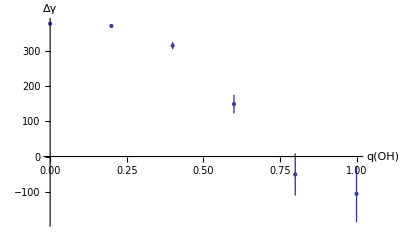

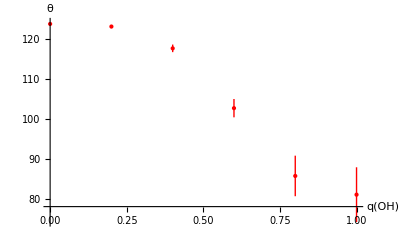

```mathematica
sl1=ErrorListPlot[Tabγ,PlotRange->All,AxesLabel->{"q(OH)","Δγ"}]
sl2=ErrorListPlot[Tabθ,PlotRange->All,AxesLabel->{"q(OH)","θ"},PlotStyle->RGBColor[1,0,0]]
```

```mathematica
√(2 0.072 (1-Cos[107 π/180])/(9.8 1000))
```

0.00435775

```mathematica
Tabθ
```

{{1.,82.8646,0.18114},{0.8,87.6266,1.57926},{0.6,103.111,0.517614},{0.4,117.321,0.412198},{0.2,123.492,0.601091},{0.,123.866,0.60676}}

```mathematica
(* Export angles *)
Export["~/Documents/Raziskave/Gromacs/BergLimit/DataFig/contact-freeze-q.dat",Append[Tabθ,{}]]
```

~/Documents/Raziskave/Gromacs/BergLimit/DataFig/contact-freeze-q.dat

## Surfac-water-air (films)

```mathematica
Tab1=Sort[Import["~/.wine/drive_c/BergLimit/SWA2.6r.dat"]];
```

```mathematica
Tab1
```

{{0,999.856,7.54289},{2,988.778,9.02246},{4,1008.39,7.92378},{6,1020.18,8.00258},{8,1016.2,8.28212},{10,996.225,8.34353},{13,1001.87,9.4497},{15,1053.16,10.9105},{20,1043.95,12.0596},{30,1028.99,10.0986},{40,974.931,11.5709},{50,968.131,13.8387},{70,951.531,11.6055},{100,917.501,9.29634},{150,1041.17,33.3254},{200,954.048,9.23833},{300,973.091,59.4917}}

```mathematica
Nlip=200;
Tab2=Table[{Tab1[[i,1]]/Nlip,Tab1[[i,2]]/2,Tab1[[i,3]]/2},{i,1,Length[Tab1]}];
```

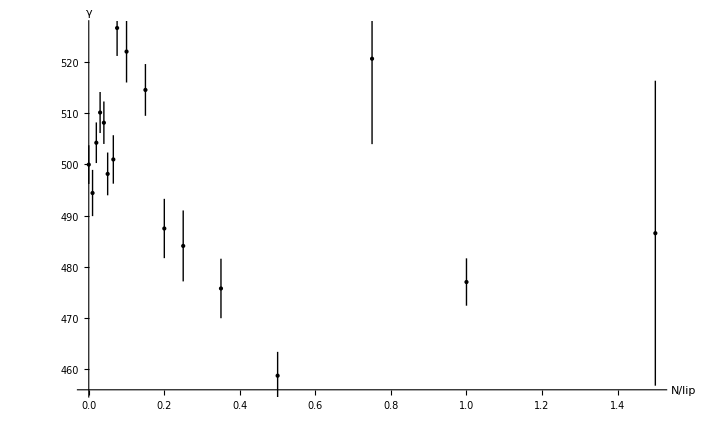

```mathematica
sl=ErrorListPlot[Tab2,AxesLabel->{"N/lip","γ"},PlotStyle->RGBColor[0.,0.,0.]]
```

```mathematica
Export["/Users/kanduc/Documents/Raziskave/Gromacs/BergLimit/DataFig/SWA2.6r.dat",Append[Sort[Tab2],{}]//N]
```

/Users/kanduc/Documents/Raziskave/Gromacs/BergLimit/DataFig/SWA2.6r.dat

```mathematica
Append[Sort[Tab2],{}]
```

{{0,746.52,4.82402},{1/100,840.225,4.97442},{1/50,1011.14,6.31585},{3/100,978.695,5.92985},{1/25,980.35,6.7217},{1/20,992.895,7.05115},{13/200,983.065,7.0177},{3/40,1024.66,8.12835},{1/10,993.48,8.08995},{3/20,941.7,9.4729},{1/5,930.03,9.08635},{1/4,893.135,8.0846},{7/20,869.42,8.2347},{1/2,867.17,9.28375},{3/4,820.31,9.3866},{1,800.695,7.5647},{3/2,821.755,8.70665},{}}

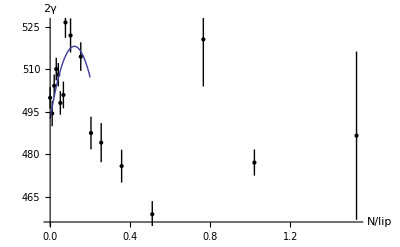

518.134

```mathematica
TabFit=Table[{Tab2[[i,1]],Tab2[[i,2]]},{i,2,10}];
pfit[x0_]=Fit[TabFit,{1,x,x^2},x]/.x->x0;
picfit=Plot[pfit[x0],{x0,0,0.2}];
Show[sl,picfit]
FindMaximum[pfit[x0],x0][[1]]
```

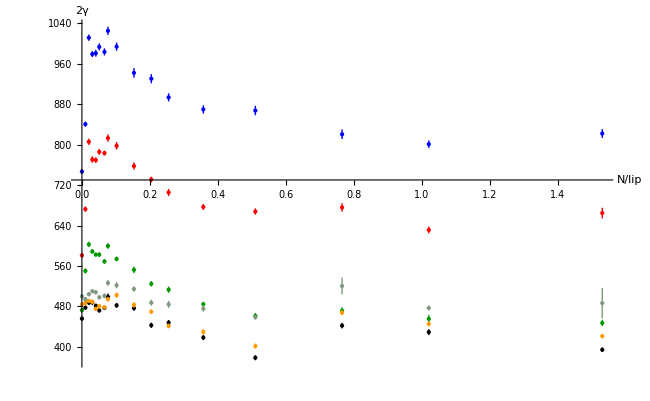

```mathematica
Show[sl1,sl2,sl3,sl4,sl5,sl6,PlotRange->All]
```

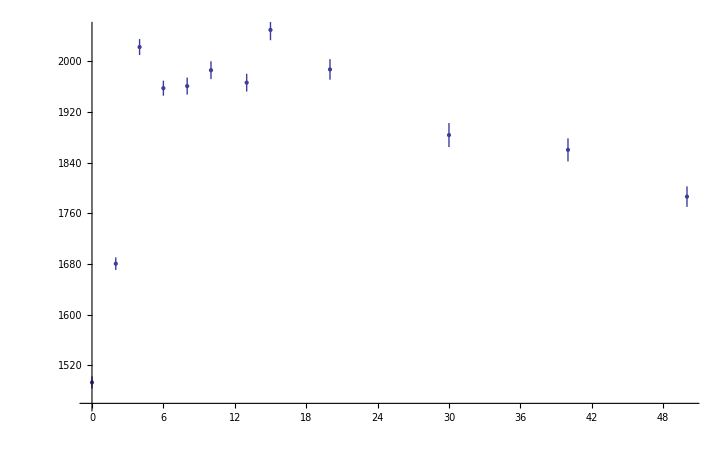

```mathematica
Take[Tab1,{1,12}]//ErrorListPlot
```

```mathematica
Tab1
```

{{0,1493.04,9.64804},{2,1680.45,9.94883},{4,2022.28,12.6317},{6,1957.39,11.8597},{8,1960.7,13.4434},{10,1985.79,14.1023},{13,1966.13,14.0354},{15,2049.32,16.2567},{20,1986.96,16.1799},{30,1883.4,18.9458},{40,1860.06,18.1727},{50,1786.27,16.1692},{70,1738.84,16.4694},{100,1734.34,18.5675},{150,1640.62,18.7732},{200,1601.39,15.1294},{300,1643.51,17.4133}}

```mathematica
1493/2.
```

746.5

```mathematica
(2000-312)/550.
```

3.06909

```mathematica
(* num of H-bonds between XOH-XOH *)
TabH1=Sort[Import["~/Documents/Raziskave/Gromacs/BergLimit/DataFig/SWA2-Hbonds.1r.dat"]];
```

```mathematica
TabH1
```

{{0,16.7037,0.0967767},{2,17.6247,0.120126},{4,18.1602,0.100811},{6,17.761,0.118585},{8,17.3957,0.114144},{10,16.9737,0.112114},{13,16.4629,0.120521},{15,16.4437,0.115578},{20,14.7543,0.0999586},{30,12.5071,0.133324},{40,10.6047,0.0902781},{50,8.85033,0.0758443},{70,6.3141,0.0816298},{100,4.00777,0.0484972},{150,1.565,0.0443859},{200,0.858737,0.0206687},{300,0.487684,0.0115792}}

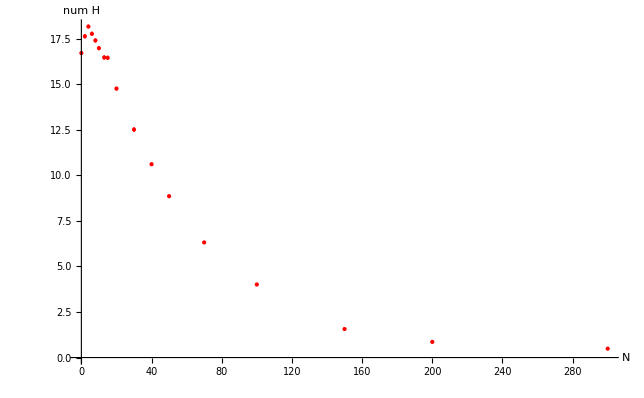

```mathematica
ErrorListPlot[TabH1,AxesLabel->{"N","num H"},PlotStyle->Red]
```

### Case of hard surfaces (take first in SWA2.1g.dat)

```mathematica
TabSW=Sort[Import["~/.wine/drive_c/BergLimit/SWA2.1g.dat"]]
```

```mathematica
Tab1=Sort[Import["~/.wine/drive_c/BergLimit/SWA2.1g.dat"]]
```

{{10,4418.26,19.0022},{15,4406.82,15.5959},{20,4361.67,22.0019},{25,4344.96,21.1441},{30,4286.43,17.3071}}